メゾンMを入れたポテンシャルのmoduli stabilization

```mathematica
ClearAll;
inittime=AbsoluteTime[];
zero[x_]=0;

W=w0+A Exp[-a T]+B Exp[-b T]+μ X M+α Λ^3*Exp[-c T]/M^(1/(n-1));
W̄=W/.{T->T̄,X->X̄,M->M̄};

K=-3Log[T+T̄]+Z X*X̄+μ M*M̄;

Subscript[W, T]=D[W,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T]=D[K,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄]=D[K,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, M]=D[W,M]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M]=D[K,M]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M̄]=D[K,M̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, X]=D[W,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X]=D[K,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄]=D[K,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T T̄]=D[K,T,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M M̄]=D[K,M,M̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X X̄]=D[K,X,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T X̄]=D[K,T,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T M̄]=D[K,T,M̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X T̄]=D[K,X,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X M̄]=D[K,X,M̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M T̄]=D[K,M,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M X̄]=D[K,M,X̄]/.{OverBar'->zero,OverBar''->zero};

DTW=Subscript[W, T]+Subscript[K, T]*W;
OverBar[DTW]=DTW/.{T->T̄,T̄->T,X->X̄,X̄->X,M->M̄,M̄->M};
DXW=Subscript[W, X]+Subscript[K, X]*W;
OverBar[DXW]=DXW/.{T->T̄,T̄->T,X->X̄,X̄->X,M->M̄,M̄->M};
DMW=Subscript[W, M]+Subscript[K, M]*W;
OverBar[DMW]=DMW/.{T->T̄,T̄->T,X->X̄,X̄->X,M->M̄,M̄->M};

Kmat={{Subscript[K, T T̄],Subscript[K, T X̄],Subscript[K, T M̄]},{Subscript[K, X T̄],Subscript[K, X X̄],Subscript[K, X M̄]},{Subscript[K, M T̄],Subscript[K, M X̄],Subscript[K, M M̄]}};
Kinv=Inverse[Kmat];
Subscript[invK, T T̄]=Kinv[[1,1]];
Subscript[invK, T X̄]=Kinv[[1,2]];
Subscript[invK, T M̄]=Kinv[[1,3]];
Subscript[invK, X T̄]=Kinv[[2,1]];
Subscript[invK, X X̄]=Kinv[[2,2]];
Subscript[invK, X M̄]=Kinv[[2,3]];
Subscript[invK, M T̄]=Kinv[[3,1]];
Subscript[invK, M X̄]=Kinv[[3,2]];
Subscript[invK, M M̄]=Kinv[[3,3]];

vtemp=Exp[K]*(Subscript[invK, T T̄]*(DTW)*(OverBar[DTW])+Subscript[invK, T X̄]*(DTW)*(OverBar[DXW])+Subscript[invK, T M̄]*(DTW)*(OverBar[DMW])+Subscript[invK, X T̄]*(DXW)*(OverBar[DTW])+Subscript[invK, X X̄]*(DXW)*(OverBar[DXW])+Subscript[invK, X M̄]*(DXW)*(OverBar[DMW])+Subscript[invK, M T̄]*(DMW)*(OverBar[DTW])+Subscript[invK, M X̄]*(DMW)*(OverBar[DXW])+Subscript[invK, M M̄]*(DMW)*(OverBar[DMW])-3W*W̄);
Print["V=",vtemp];

V=ComplexExpand[vtemp/.{T->ReT+I ImT,T̄->ReT-I ImT,X->ReX+I ImX,X̄->ReX-I ImX,M->ReM+I ImM,M̄->ReM-I ImM}];

Clear[w0];
w0=-Abs[A Abs[a A/(b B)]^(a/(b-a))+B Abs[a A/(b B)]^(b/(b-a))]+δw0;

valδw0=0;
vala=2Pi/100;
valb=2Pi/99;
valA=1;
valB=-1.03;

valn=2;
valΛ=10^(-3);
valC=1;
valλ=1;
valZ=1;

valμ=valλ*valΛ;
valα=valC*valΛ^(1/(valn-1));

(* mixing for moduli and mesons *)
valc=2Pi;

(* remove the dependence of the imaginary and insert parameters *)
V=Expand[V/.{ImM->0,ImX->0,ImT->0}/.{α->valα,n->valn,μ->valμ,Λ->valΛ,λ->valλ,Z->valZ}/.{a->vala,b->valb,A->valA,B->valB,c->valc,δw0->valδw0}/.Arg->zero];
Print["time: ",AbsoluteTime[]-inittime];
```

V=1/(T+T̄)^3 ⅇ^(M μ M̄+X Z X̄) (-3 (A ⅇ^(-a T)+B ⅇ^(-b T)+w0+ⅇ^(-c T) M^(-1/(-1+n)) α Λ^3+M X μ) (A ⅇ^(-a T̄)+B ⅇ^(-b T̄)+w0+ⅇ^(-c T̄) α Λ^3 (M̄)^(-1/(-1+n))+μ M̄ X̄)+((M μ+Z (A ⅇ^(-a T)+B ⅇ^(-b T)+w0+ⅇ^(-c T) M^(-1/(-1+n)) α Λ^3+M X μ) X̄) (μ M̄+X Z (A ⅇ^(-a T̄)+B ⅇ^(-b T̄)+w0+ⅇ^(-c T̄) α Λ^3 (M̄)^(-1/(-1+n))+μ M̄ X̄)))/Z+1/μ(-(ⅇ^(-c T) M^(-1-1/(-1+n)) α Λ^3)/(-1+n)+X μ+μ (A ⅇ^(-a T)+B ⅇ^(-b T)+w0+ⅇ^(-c T) M^(-1/(-1+n)) α Λ^3+M X μ) M̄) (-(ⅇ^(-c T̄) α Λ^3 (M̄)^(-1-1/(-1+n)))/(-1+n)+μ X̄+M μ (A ⅇ^(-a T̄)+B ⅇ^(-b T̄)+w0+ⅇ^(-c T̄) α Λ^3 (M̄)^(-1/(-1+n))+μ M̄ X̄))+1/3 (T+T̄)^2 (-a A ⅇ^(-a T)-b B ⅇ^(-b T)-c ⅇ^(-c T) M^(-1/(-1+n)) α Λ^3-(3 (A ⅇ^(-a T)+B ⅇ^(-b T)+w0+ⅇ^(-c T) M^(-1/(-1+n)) α Λ^3+M X μ))/(T+T̄)) (-a A ⅇ^(-a T̄)-b B ⅇ^(-b T̄)-c ⅇ^(-c T̄) α Λ^3 (M̄)^(-1/(-1+n))-(3 (A ⅇ^(-a T̄)+B ⅇ^(-b T̄)+w0+ⅇ^(-c T̄) α Λ^3 (M̄)^(-1/(-1+n))+μ M̄ X̄))/(T+T̄)))

time: 0.4506708

```mathematica
(* stabilized by KL moudli potential *)
Vkl=Expand[V/.{ReT->62.4}];

Print[
Plot3D[Vkl,{ReX,-1,1},{ReM,10^(-6),1},Axes->True,AxesLabel->{"X","M"}]
];

(* stabilized by remaing variables*)
Block[{$MaxPrecision=Infinity},
sol=FindMinimum[Vkl,{ReX,10^(-4)},{ReM,10^(-4)},WorkingPrecision->600,AccuracyGoal->40];
];

Print[N[sol[[1]],3]];
Print[N[sol[[2]][[1]],3],", ",N[sol[[2]][[2]],3]];

rexmid=ReX/.sol[[2]];
remmid=ReM/.sol[[2]];

Print["V_min=",Vkl/.{ReX->rexmid,ReM->remmid}];

Print[
ContourPlot[Subscript[V, kl],{ReX,rexmid-10^(-6),rexmid+10^(-6)},{ReM,remmid-10^(-6),remmid+10^(-6)},Axes->True]
];
```

General::munfl: Exp[-784.142]は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::stop: この計算中に，General::munflのこれ以上の出力は表示されません．

-Graphics3D-

FindMinimum::precw: 引数関数(1.50785×10^-19 ⅇ^(ReM^2/1000+ReX^2)+(1.95309×10^-199 ⅇ^(ReM^2/1000+ReX^2))/ReM+5.14465×10^-13 ⅇ^(ReM^2/1000+ReX^2) ReM^2-(1.34654×10^-192 ⅇ^(ReM^2/1000+ReX^2))/(√(ReM^2))-1.95309×10^-202 ⅇ^(ReM^2/1000+ReX^2) √(ReM^2)-5.4729×10^-192 ⅇ^((«1»)/(«4»)+«1») ReX-(5.4729×10^-189 ⅇ^(«1»+«1») ReX)/ReM^2-9.64809×10^-16 ⅇ^(ReM^2/1000+ReX^2) ReM ReX-3.67198×10^-23 ⅇ^(ReM^2/1000+ReX^2) ReM^3 ReX+(4.30247×10^-189 ⅇ^(ReM^2/1000+ReX^2) √(ReM^2) ReX)/ReM+«8»)の精度がWorkingPrecision (600.)より小さくなっています．

1.51×10^-19

ReX→1.33×10^-41, ReM→4.23×10^-41

General::munfl: 2.31283×10^-235 «636»は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::munfl: 1.29506×10^-151 «650»は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

V_min=1.50785×10^-19

-Graphics-

陳さんの修論の結果を再現

```mathematica
ClearAll;
inittime=AbsoluteTime[];
zero[x_]=0;

W=w0+μ X M+α Λ^3/M^(1/(n-1));
W̄=W/.{X->X̄,M->M̄};

Print["W=",W];

K=Z X X̄+μ M M̄;

Print["K=",K];

Subscript[W, M]=D[W,M]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M]=D[K,M]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M̄]=D[K,M̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, X]=D[W,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X]=D[K,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄]=D[K,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M M̄]=D[K,M,M̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X X̄]=D[K,X,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X M̄]=D[K,X,M̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M X̄]=D[K,M,X̄]/.{OverBar'->zero,OverBar''->zero};
DXW=Subscript[W, X]+Subscript[K, X]*W;
OverBar[DXW]=DXW/.{X->X̄,X̄->X,M->M̄,M̄->M};
DMW=Subscript[W, M]+Subscript[K, M]*W;
OverBar[DMW]=DMW/.{X->X̄,X̄->X,M->M̄,M̄->M};

Kmat={{Subscript[K, X X̄],Subscript[K, M X̄]},{Subscript[K, X M̄],Subscript[K, M M̄]}};
Kinv=Inverse[Kmat];

Subscript[invK, X X̄]=Kinv[[1,1]];
Subscript[invK, X M̄]=Kinv[[1,2]];
Subscript[invK, M X̄]=Kinv[[2,1]];
Subscript[invK, M M̄]=Kinv[[2,2]];

vtemp=Exp[K]*(Subscript[invK, X X̄]*(DXW)*(OverBar[DXW])+Subscript[invK, X M̄]*(DXW)*(OverBar[DMW])+Subscript[invK, M X̄]*(DMW)*(OverBar[DXW])+Subscript[invK, M M̄]*(DMW)*(OverBar[DMW])-3W*W̄);
Print["V=",vtemp];

V=ComplexExpand[vtemp/.{X->ReX+I ImX,X̄->ReX-I ImX,M->ReM+I ImM,M̄->ReM-I ImM}];
(* Print["V=",V]; *)

Print["time: ",AbsoluteTime[]-inittime];
```

W=w0+M^(-1/(-1+n)) α Λ^3+M X μ

K=M μ M̄+X Z X̄

V=ⅇ^(M μ M̄+X Z X̄) (-3 (w0+M^(-1/(-1+n)) α Λ^3+M X μ) (w0+α Λ^3 (M̄)^(-1/(-1+n))+μ M̄ X̄)+((M μ+Z (w0+M^(-1/(-1+n)) α Λ^3+M X μ) X̄) (μ M̄+X Z (w0+α Λ^3 (M̄)^(-1/(-1+n))+μ M̄ X̄)))/Z+((-(M^(-1-1/(-1+n)) α Λ^3)/(-1+n)+X μ+μ (w0+M^(-1/(-1+n)) α Λ^3+M X μ) M̄) (-(α Λ^3 (M̄)^(-1-1/(-1+n)))/(-1+n)+μ X̄+M μ (w0+α Λ^3 (M̄)^(-1/(-1+n))+μ M̄ X̄)))/μ)

time: 0.0680232

1.65×10^-12

ReX→0.000758, ReM→0.00115

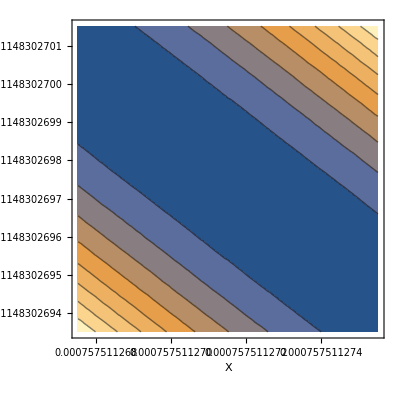

time: 8.5640463

```mathematica
inittime=AbsoluteTime[];
valw0=10^(-16);
valn=2;
valΛ=10^(-3);
valC=1;
valλ=1;
valZ=1;

valμ=valλ*valΛ;
valα=valC*valΛ^(1/(valn-1));

sol=FindMinimum[(ReX^4+V)/.{ImM->0,ImX->0}/.Arg->zero/.{α->valα,n->valn,μ->valμ,Λ->valΛ,λ->valλ,Z->valZ,w0->valw0},{ReX,10^(-4)},{ReM,10^(-4)},WorkingPrecision->600,AccuracyGoal->40,PrecisionGoal->Infinity,MaxIterations->300,Method->"Newton"];

Print[N[sol[[1]],3]];
Print[N[sol[[2]][[1]],3],", ",N[sol[[2]][[2]],3]];

rexmid=ReX/.sol[[2]];
remmid=ReM/.sol[[2]];

plran=4*10^(-12);

Print[
ContourPlot[(ReX^4+V)*10^(25)/.{ImM->0,ImX->0}/.Arg->zero/.{α->valα,n->valn,μ->valμ,Λ->valΛ,λ->valλ,Z->valZ,w0->valw0},{ReX,rexmid-plran,rexmid+plran},{ReM,remmid-plran,remmid+plran},Axes->True,AxesLabel->{"X","M"},PlotPoints->10,WorkingPrecision->100]
];

Print["time: ",AbsoluteTime[]-inittime];
```

KL problemのチェック

```mathematica
ClearAll;

zero[x_]=0;

W=w0+A Exp[-a T]+B Exp[-b T];
W̄=W/.{T->T̄};
K=-3Log[T+T̄];

Subscript[W, T]=D[W,T]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, T]=D[K,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄]=D[K,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T T̄]=D[K,T,T̄]/.{OverBar'->zero,OverBar''->zero};
DTW=Subscript[W, T]+Subscript[K, T]*W;
OverBar[DTW]=DTW/.{T->T̄,T̄->T};

vtemp=Exp[K]*((Subscript[K, T T̄])^(-1)*(DTW)*(OverBar[DTW])-3W*W̄);
Print["V=",vtemp];

V=FullSimplify@ComplexExpand[vtemp/.{T->ReT+I ImT,T̄->ReT-I ImT}];
Print["V=",V];V=FullSimplify[V/.{ImT->0,w0->-Abs[A Abs[a A/(b B)]^(a/(b-a))+B Abs[a A/(b B)]^(b/(b-a))]+δw0}];
Print["V=",V];
```

V=(-3 (A ⅇ^(-a T)+B ⅇ^(-b T)+w0) (A ⅇ^(-a T̄)+B ⅇ^(-b T̄)+w0)+1/3 (T+T̄)^2 (-a A ⅇ^(-a T)-b B ⅇ^(-b T)-(3 (A ⅇ^(-a T)+B ⅇ^(-b T)+w0))/(T+T̄)) (-a A ⅇ^(-a T̄)-b B ⅇ^(-b T̄)-(3 (A ⅇ^(-a T̄)+B ⅇ^(-b T̄)+w0))/(T+T̄)))/(T+T̄)^3

V=(ⅇ^(-2 (a+b) ReT) (a A^2 ⅇ^(2 b ReT) (3+a ReT)+b B^2 ⅇ^(2 a ReT) (3+b ReT)+ⅇ^((a+b) ReT) (3 a A ⅇ^(b ReT) w0 Cos[a ImT]+A B (3 (a+b)+2 a b ReT) Cos[(a-b) ImT]+3 b B ⅇ^(a ReT) w0 Cos[b ImT])))/(6 ReT^2)

V=(ⅇ^(-2 (a+b) ReT) (b B ⅇ^(a ReT)+a A ⅇ^(b ReT)) (B ⅇ^(a ReT) (3+b ReT)+ⅇ^(b ReT) (3 A+a A ReT+3 ⅇ^(a ReT) δw0)-3 ⅇ^((a+b) ReT) Abs[Abs[(a A)/(b B)]^(-b/(a-b)) (B+A Abs[(b B)/(a A)])]))/(6 ReT^2)

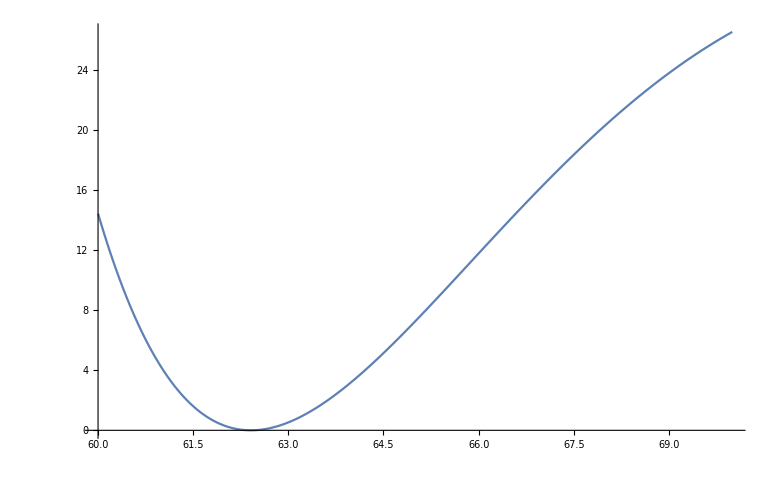

W=-2.22045×10^-16

```mathematica
valδw0=0;
vala=2Pi/100;
valb=2Pi/99;
valA=1;
valB=-1.03;

init=60;

Print[
Plot[V*10^(15)/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0},{ReT,init,init+10},WorkingPrecision->100,PlotPoints->200]
];

sol=FindMinimum[V*10^(10)/.w0->-Abs[A Abs[a A/(b B)]^(a/(b-a))+B Abs[a A/(b B)]^(b/(b-a))]+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0},{ReT,62,70},PrecisionGoal->Infinity];
valT=ReT/.sol[[2]];

Print["W=",W/.w0->-Abs[A Abs[a A/(b B)]^(a/(b-a))+B Abs[a A/(b B)]^(b/(b-a))]+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}/.T->valT];
```

KKLT

```mathematica
ClearAll;

zero[x_]=0;

W=w0+A Exp[-a T];
W̄=W/.{T->T̄};
K=-3Log[T+T̄];

Subscript[W, T]=D[W,T]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, T]=D[K,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄]=D[K,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T T̄]=D[K,T,T̄]/.{OverBar'->zero,OverBar''->zero};
DTW=Subscript[W, T]+Subscript[K, T]*W;
OverBar[DTW]=DTW/.{T->T̄,T̄->T};

vtemp=Exp[K]*((Subscript[K, T T̄])^(-1)*(DTW)*(OverBar[DTW])-3W*W̄);
Print["V=",vtemp];

V=FullSimplify@ComplexExpand[vtemp/.{T->ReT+I ImT,T̄->ReT-I ImT}];
Print["V=",V];
```

V=(-3 (A ⅇ^(-a T)+w0) (A ⅇ^(-a T̄)+w0)+1/3 (T+T̄)^2 (-a A ⅇ^(-a T)-(3 (A ⅇ^(-a T)+w0))/(T+T̄)) (-a A ⅇ^(-a T̄)-(3 (A ⅇ^(-a T̄)+w0))/(T+T̄)))/(T+T̄)^3

V=(a A ⅇ^(-2 a ReT) (A (3+a ReT)+3 ⅇ^(a ReT) w0 Cos[a ImT]))/(6 ReT^2)

```mathematica
V=FullSimplify[V/.{ImT->Pi/a,w0->Abs[A Abs[a A/(b B)]^(a/(b-a))+B Abs[a A/(b B)]^(b/(b-a))]}];
Print["V=",V];
```

V=(a A ⅇ^(-2 a ReT) (A (3+a ReT)-3 ⅇ^(a ReT) Abs[A Abs[(a A)/(b B)]^(a/(-a+b))+B Abs[(a A)/(b B)]^(b/(-a+b))]))/(6 ReT^2)

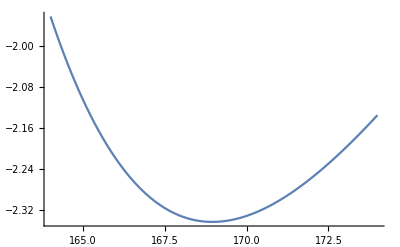

```mathematica
vala=2Pi/100;
valb=2Pi/99;
valA=1;
valB=-1.03;

init=164;
Plot[V*10^(15)/.{a->vala,b->valb,A->valA,B->valB},{ReT,init,init+10},WorkingPrecision->100,PlotPoints->200]
```